# Serienschwingkreis

## Funktionen

### Includes

```mathematica
<<"Labor.m"
Needs["ErrorBarPlots`"]
Needs["ErrorBarLogPlots`"]
Gauss[a_]:= Module[{},{Mean[a],StandardDeviation[a]/Sqrt[Length[a]]}];
```

## Geräteliste

Oszi:
true rms:

## 1.) Resonanzfrequenz (Bestimmung aus Phasenverlauf am Widerstand)

### Induktivität und Kapazität

```mathematica
l={5.6,0}*10^-3;
rl=0.83;
c={0.15,0}*10^-6;
r={10,0};
```

### Theoretische Resonanzfrequenz

```mathematica
f0=(Elec`Fω[l[[1]],l[[2]],c[[1]],c[[2]]])/(2*π)
```

{5491.37,0}

### Frequenzverteilung

```mathematica
f=Join[Table[f0[[1]]-f0[[1]]*10^Log[x/6],{x,1,6}],{f0[[1]]}];
f = Join[f,Table[f0[[1]]+f0[[1]]*10^Log[x/6],{x,1,6}]]//Sort
```

{0.,1882.6,3332.55,4378.27,5053.78,5402.67,5491.37,5580.07,5928.96,6604.46,7650.18,9100.13,10982.7}

```mathematica
1/(2*π)*√(1/(l[[1]]*c[[1]])-rl^2/l[[1]]^2)
```

5491.32

### Theroretische Güte Q

```mathematica
Elec`FQ[r[[1]],r[[2]],l[[1]],l[[2]],c[[1]],c[[2]]]
```

Elec`FQ[10,0,0.0056,0,1.5×10^-7,0]

```mathematica
Begin["R`"];
```

### Messung (Achtung! Konstante Eingangsspannung von 2 V Spitze-Spitze, manuell nachregeln!)

```mathematica
M={{"f/Hz", "Ua/V", "δt", "Ue/V"}, {1906, 1.4*2*20*10^-3, 1.4*0.1*10^-3, 4*0.5}, {3349, 1.4*2*50*10^-3, 1.4*50*10^-6, 4*0.5}, {4440, 1.6*2*0.1, 0.9*50*10^-6, 4*0.5}, {5000, 1.6*2*0.2, 0.5*50*10^-6, 4*0.5}, {5410, 2*2*0.2, 0.5*5*10^-6, 4*0.5}, {5491, 2*2*0.2, -0.6*10*10^-6, 4*0.5}, {5580, 1.8*2*0.2, -1.2*10*10^-6, 4*0.5}, {5.93*10^3, 1.3*2*0.2, -1.1*20*10^-6, 4*0.5}, {6.60*10^3, 0.8*2*0.2, -1.3*20*10^-6, 4*0.5}, {7.63*10^3, 0.9*2*0.1, -1.3*20*10^-6, 4*0.5}, {9.10*10^3, 1.1*2*50*10^-3, -1.1*20*10^-6, 4*0.5}, {11.00*10^3, 0.9*2*50*10^-3, -1*20*10^-6, 4*0.5}, {30.22*10^3, 0.7*2*20*10^-3, -1.4*5*10^-6, 4*0.5}}; dM={{"Δf/Hz", "ΔUa/V", "Δδt", "ΔUe/V"}, {□, □, □, 0.1}, {□, □, □, 0.1}, {□, □, □, 0.1}, {□, □, □, 0.1}, {□, □, □, 0.1}, {□, □, □, 0.1}, {□, □, □, 0.1}, {□, □, □, 0.1}, {□, □, □, 0.1}, {□, □, □, 0.1}, {□, □, □, 0.1}, {□, □, □, 0.1}, {□, □, □, 0.1}, {□, □, □, 0.1}, {□, □, □, 0.1}, {□, □, □, 0.1}, {□, □, □, 0.1}, {□, □, □, 0.1}, {□, □, □, 0.1}};

Ue=4;(*eff, fluke 175*)
due=0.4;
```

### Amplitudengang

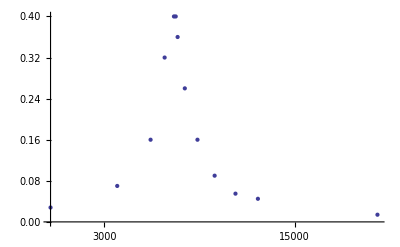

```mathematica
ListLogLinearPlot[Table[{M[[x,1]], M[[x,2]]/M[[x,4]]},{x,2,Length[M]}]]
```

```mathematica
At=Table[Basic`Fdiv[M[[x,2]],dM[[x,2]],M[[x,4]],dM[[x,4]]],{x,2,Length[M]}];
p1 = Table[{{M[[x,1]],10 Log[At[[x-1,1]]]},ErrorBar[dM[[x,1]],At[[x-1,2]]]},{x,2,Length[M]}];
```

```mathematica
Show[ErrorListLogLinearPlot[p1,Joined-> True,PlotStyle-> {Blue}],
LogLinearPlot[{{-3},{0}},{x,Min[M[[2;;Length[M],1]]],Max[M[[2;;Length[M],1]]]},PlotStyle-> {Orange,Black}],
(*ListLogLinearPlot[{{9233.33,10},{9233.33,-50}},Joined ->True,PlotStyle-> {Brown}],*)
AxesLabel -> {"f/Hz","Dämpfung/dB"}]
```

LogLinearPlot::llplim: Range specification {x, Min[M ⟦ 2 ;; Length[M], 1 ⟧], Max[M ⟦ 2 ;; Length[M], 1 ⟧]} is not of the form {x, xmin, xmax} with xmin and xmax positive.

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics-,LogLinearPlot[{{-3},{0}},{x,Min[M⟦2;;Length[M],1⟧],Max[M⟦2;;Length[M],1⟧]},PlotStyle→{Orange,Black}],AxesLabel→{f/Hz,Dämpfung/dB}]

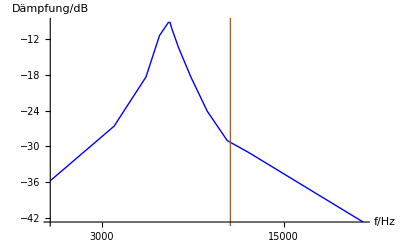

```mathematica
Show[ListLogLinearPlot[Table[{M[[x,1]],10 Log[M[[x,2]]/M[[x,4]]]},{x,2,Length[M]}],Joined-> True,PlotStyle-> {Blue}],
LogLinearPlot[{{-3},{0}},{x,Min[M[[2;;Length[M],1]]],Max[M[[2;;Length[M],1]]]},PlotStyle-> {Orange,Black}],
ListLogLinearPlot[{{9360,10},{9360,-50}},Joined ->True,PlotStyle-> {Brown}],
AxesLabel -> {"f/Hz","Dämpfung/dB"}]
```

### Phasengang

```mathematica
ϕ=Table[Basic`Fmult[M[[x,3]],dM[[x,3]],M[[x,1]],dM[[x,1]]]*360,{x,2,Length[M]}];
p2 = Table[{{M[[x,1]],ϕ[[x-1,1]]},ErrorBar[dM[[x,1]],ϕ[[x-1,2]]]},{x,2,Length[M]}];
```

LogLinearPlot::llplim: Range specification {x, Min[M ⟦ 2 ;; Length[M], 1 ⟧], Max[M ⟦ 2 ;; Length[M], 1 ⟧]} is not of the form {x, xmin, xmax} with xmin and xmax positive.

Show::gcomb: Could not combine the graphics objects in ….

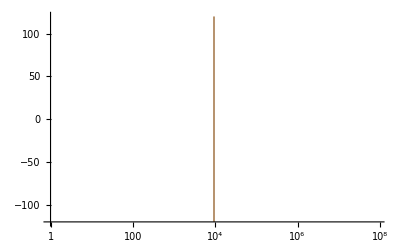
Show[-Graphics-,LogLinearPlot[{{0}},{x,Min[M⟦2;;Length[M],1⟧],Max[M⟦2;;Length[M],1⟧]},PlotStyle→{Orange}],-Graphics-,AxesLabel→{f/Hz,ϕ/°}]

```mathematica
Show[ErrorListLogLinearPlot[p2,Joined-> True,PlotStyle-> {Blue}],
LogLinearPlot[{{0}},{x,Min[M[[2;;Length[M],1]]],Max[M[[2;;Length[M],1]]]},PlotStyle-> {Orange}],
ListLogLinearPlot[{{9360,-120},{9360,120}},Joined ->True,PlotStyle-> {Brown}],
AxesLabel-> {"f/Hz","ϕ/°"}]
```

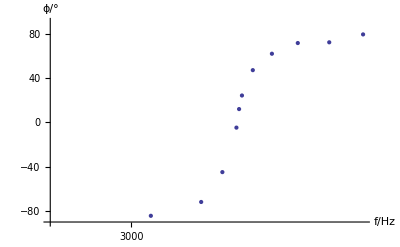

```mathematica
p3=Table[{M[[x,1]],-M[[x,1]]*M[[x,3]]*360},{x,2,Length[M]-1}];
ListLogLinearPlot[p3,AxesLabel-> {"f/Hz","ϕ/°"},PlotRange-> {{0,10^6},{-90,90}}]
```

## Amplitudengang und Phasengang der Induktivität

```mathematica
Begin["I`"];
```

### Messung (Achtung! Konstante Eingangsspannung von 2 V Spitze-Spitze, manuell nachregeln!)

```mathematica
M={{"f/Hz", "Ua/V", "δt", "Ue/V"}, {1906, 1.4*2*0.1, 1.3*0.2*10^-3, 4*0.5}, {3349, 3.1*2*0.2, 2.8*50*10^-6, 4*0.5}, {4440, 2.1*2*1, 2*50*10^-6, 4*0.5}, {5000, 2.3*2*2, 1.4*50*10^-6, 4*0.5}, {5410, 3.2*2*2, 0.8*50*10^-6, 4*0.5}, {5491, 3.2*2*2, 0.7*50*10^-6, 4*0.5}, {5580, 2.9*2*2, 0.6*50*10^-6, 4*0.5}, {5.93*10^3, 2.1*2*2, 0.4*50*10^-6, 4*0.5}, {6.60*10^3, 2.7*2*1, 0.4*20*10^-6, 4*0.5}, {7.63*10^3, 2*2*1, 0.2*20*10^-6, 4*0.5}, {9.10*10^3, 1.6*2*1, 0.3*10*10^-6, 4*0.5}, {11.00*10^3, 1.3*2*1, 0.4*5*10^-6, 4*0.5}, {30.22*10^3, 2.1*2*0.5, 0, 4*0.5}}; dM={{"Δf/Hz", "ΔUa/V", "Δδt", "ΔUe/V"}, {1, 0.02, □, 0.1}, {1, 0.04, □, 0.1}, {1, 0.2, □, 0.1}, {1, 0.4, □, 0.1}, {1, 0.4, □, 0.1}, {1, 0.4, □, 0.1}, {1, 0.4, □, 0.1}, {10, 0.4, □, 0.1}, {10, 0.2, □, 0.1}, {10, 0.2, □, 0.1}, {10, 0.2, □, 0.1}, {10, 0.2, □, 0.1}, {10, 0.1, 10^-6/5, 0.1}};

Ue=4;(*eff, fluke 175*)
due=0.4;
```

### Amplitudengang

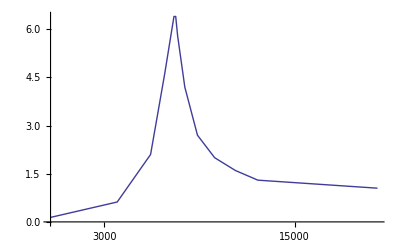

```mathematica
ListLogLinearPlot[Table[{M[[x,1]], M[[x,2]]/M[[x,4]]},{x,2,Length[M]}],Joined -> True]
```

```mathematica
At=Table[Basic`Fdiv[M[[x,2]],dM[[x,2]],M[[x,4]],dM[[x,4]]],{x,2,Length[M]}];
p1 = Table[{{M[[x,1]],10 Log[At[[x-1,1]]]},ErrorBar[dM[[x,1]],At[[x-1,2]]]},{x,2,Length[M]}];
```

```mathematica
Show[ErrorListLogLinearPlot[p1,Joined-> True,PlotStyle-> {Blue}],
LogLinearPlot[{{-3},{0}},{x,Min[M[[2;;Length[M],1]]],Max[M[[2;;Length[M],1]]]},PlotStyle-> {Orange,Black}],
(*ListLogLinearPlot[{{9233.33,10},{9233.33,-50}},Joined ->True,PlotStyle-> {Brown}],*)
AxesLabel -> {"f/Hz","Dämpfung/dB"}]
```

LogLinearPlot::llplim: Range specification {x, Min[M ⟦ 2 ;; Length[M], 1 ⟧], Max[M ⟦ 2 ;; Length[M], 1 ⟧]} is not of the form {x, xmin, xmax} with xmin and xmax positive.

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics-,LogLinearPlot[{{-3},{0}},{x,Min[M⟦2;;Length[M],1⟧],Max[M⟦2;;Length[M],1⟧]},PlotStyle→{Orange,Black}],AxesLabel→{f/Hz,Dämpfung/dB}]

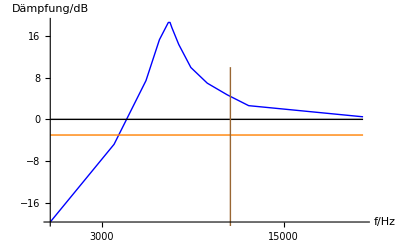

```mathematica
Show[ListLogLinearPlot[Table[{M[[x,1]],10 Log[M[[x,2]]/M[[x,4]]]},{x,2,Length[M]}],Joined-> True,PlotStyle-> {Blue}],
LogLinearPlot[{{-3},{0}},{x,Min[M[[2;;Length[M],1]]],Max[M[[2;;Length[M],1]]]},PlotStyle-> {Orange,Black}],
ListLogLinearPlot[{{9360,10},{9360,-50}},Joined ->True,PlotStyle-> {Brown}],
AxesLabel -> {"f/Hz","Dämpfung/dB"}]
```

### Phasengang

```mathematica
ϕ=Table[Basic`Fmult[M[[x,3]],dM[[x,3]],M[[x,1]],dM[[x,1]]]*360,{x,2,Length[M]}];
p2 = Table[{{M[[x,1]],ϕ[[x-1,1]]},ErrorBar[dM[[x,1]],ϕ[[x-1,2]]]},{x,2,Length[M]}];
```

```mathematica
Show[ErrorListLogLinearPlot[p2,Joined-> True,PlotStyle-> {Blue}],
LogLinearPlot[{{0}},{x,Min[M[[2;;Length[M],1]]],Max[M[[2;;Length[M],1]]]},PlotStyle-> {Orange}],
ListLogLinearPlot[{{9360,-120},{9360,120}},Joined ->True,PlotStyle-> {Brown}],
AxesLabel-> {"f/Hz","ϕ/°"}]
```

LogLinearPlot::llplim: Range specification {x, Min[M ⟦ 2 ;; Length[M], 1 ⟧], Max[M ⟦ 2 ;; Length[M], 1 ⟧]} is not of the form {x, xmin, xmax} with xmin and xmax positive.

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics-,LogLinearPlot[{{0}},{x,Min[M⟦2;;Length[M],1⟧],Max[M⟦2;;Length[M],1⟧]},PlotStyle→{Orange}],-Graphics-,AxesLabel→{f/Hz,ϕ/°}]

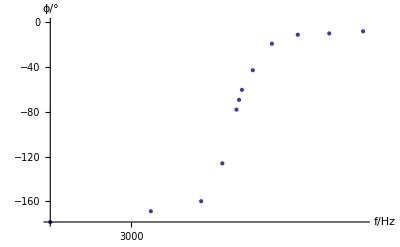

```mathematica
p3=Table[{M[[x,1]],-M[[x,1]]*M[[x,3]]*360},{x,2,Length[M]-1}];
ListLogLinearPlot[p3,AxesLabel-> {"f/Hz","ϕ/°"}]
```

```mathematica
End[];
```

## Amplitudengang und Phasengang der Kapazität

```mathematica
Begin["C`"];
```

### Messung (Achtung! Konstante Eingangsspannung von 2 V Spitze-Spitze, manuell nachregeln!)

```mathematica
M={{"f/Hz", "Ua/V", "δt", "Ue/V"}, {1906, 2.4*2*0.5, 0, 4*0.5}, {3349, 3.3*2*0.5, -0.3*20*10^-6, 4*0.5}, {4440, 3.2*2*1, -0.6*20*10^-6, 4*0.5}, {5000, 2.7*2*2, -1.3*20*10^-6, 4*0.5}, {5410, 3.2*2*2, -2.4*20*10^-6, 4*0.5}, {5491, 3*2*2, -2.6*20*10^-6, 4*0.5}, {5580, 2.8*2*2, -2.8*20*10^-6, 4*0.5}, {5.93*10^3, 3.6*2*1, -3.2*20*10^-6, 4*0.5}, {6.60*10^3, 3.7*2*0.5, -3.2*20*10^-6, 4*0.5}, {7.63*10^3, 2*2*0.5, -3.6*20*10^-6, 4*0.5}, {9.10*10^3, 3.8*2*0.2, -2.5*20*10^-6, 4*0.5}, {11.00*10^3, 3.4*2*0.1, -2.1*20*10^-6, 4*0.5}, {30.22*10^3, 2*2*20*10^-3, -3*5*10^-6, 4*0.5}}; dM={{"Δf/Hz", "ΔUa/V", "Δδt", "ΔUe/V"}, {1, 0.1, 10^-6/5, 0.1}, {1, 0.1, □, 0.1}, {1, 0.2, □, 0.1}, {1, 0.4, □, 0.1}, {1, 0.4, □, 0.1}, {1, 0.4, □, 0.1}, {1, □, □, 0.1}, {10, 0.2, □, 0.1}, {10, 0.1, □, 0.1}, {10, 0.1, □, 0.1}, {10, 0.04, □, 0.1}, {10, 0.02, □, 0.1}, {10, □, □, 0.1}};

Ue=4;(*eff, fluke 175*)
due=0.4;
```

### Amplitudengang

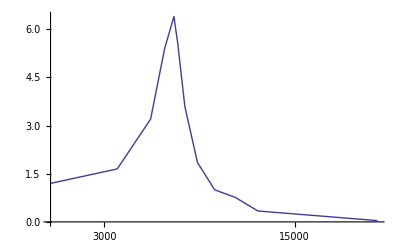

```mathematica
ListLogLinearPlot[Table[{M[[x,1]], M[[x,2]]/M[[x,4]]},{x,2,Length[M]}],Joined -> True]
```

```mathematica
At=Table[Basic`Fdiv[M[[x,2]],dM[[x,2]],M[[x,4]],dM[[x,4]]],{x,2,Length[M]}];
p1 = Table[{{M[[x,1]],10 Log[At[[x-1,1]]]},ErrorBar[dM[[x,1]],At[[x-1,2]]]},{x,2,Length[M]}];
```

```mathematica
Show[ErrorListLogLinearPlot[p1,Joined-> True,PlotStyle-> {Blue}],
LogLinearPlot[{{-3},{0}},{x,Min[M[[2;;Length[M],1]]],Max[M[[2;;Length[M],1]]]},PlotStyle-> {Orange,Black}],
(*ListLogLinearPlot[{{9233.33,10},{9233.33,-50}},Joined ->True,PlotStyle-> {Brown}],*)
AxesLabel -> {"f/Hz","Dämpfung/dB"}]
```

LogLinearPlot::llplim: Range specification {x, Min[M ⟦ 2 ;; Length[M], 1 ⟧], Max[M ⟦ 2 ;; Length[M], 1 ⟧]} is not of the form {x, xmin, xmax} with xmin and xmax positive.

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics-,LogLinearPlot[{{-3},{0}},{x,Min[M⟦2;;Length[M],1⟧],Max[M⟦2;;Length[M],1⟧]},PlotStyle→{Orange,Black}],AxesLabel→{f/Hz,Dämpfung/dB}]

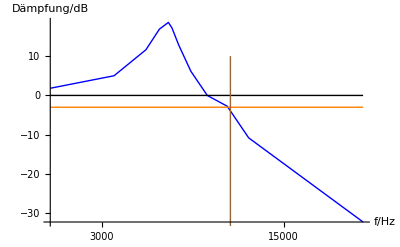

```mathematica
Show[ListLogLinearPlot[Table[{M[[x,1]],10 Log[M[[x,2]]/M[[x,4]]]},{x,2,Length[M]}],Joined-> True,PlotStyle-> {Blue}],
LogLinearPlot[{{-3},{0}},{x,Min[M[[2;;Length[M],1]]],Max[M[[2;;Length[M],1]]]},PlotStyle-> {Orange,Black}],
ListLogLinearPlot[{{9360,10},{9360,-50}},Joined ->True,PlotStyle-> {Brown}],
AxesLabel -> {"f/Hz","Dämpfung/dB"}]
```

### Phasengang

```mathematica
ϕ=Table[Basic`Fmult[M[[x,3]],dM[[x,3]],M[[x,1]],dM[[x,1]]]*360,{x,2,Length[M]}];
p2 = Table[{{M[[x,1]],ϕ[[x-1,1]]},ErrorBar[dM[[x,1]],ϕ[[x-1,2]]]},{x,2,Length[M]}];
```

```mathematica
Show[ErrorListLogLinearPlot[p2,Joined-> True,PlotStyle-> {Blue}],
LogLinearPlot[{{0}},{x,Min[M[[2;;Length[M],1]]],Max[M[[2;;Length[M],1]]]},PlotStyle-> {Orange}],
ListLogLinearPlot[{{9360,-120},{9360,120}},Joined ->True,PlotStyle-> {Brown}],
AxesLabel-> {"f/Hz","ϕ/°"}]
```

LogLinearPlot::llplim: Range specification {x, Min[M ⟦ 2 ;; Length[M], 1 ⟧], Max[M ⟦ 2 ;; Length[M], 1 ⟧]} is not of the form {x, xmin, xmax} with xmin and xmax positive.

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics-,LogLinearPlot[{{0}},{x,Min[M⟦2;;Length[M],1⟧],Max[M⟦2;;Length[M],1⟧]},PlotStyle→{Orange}],-Graphics-,AxesLabel→{f/Hz,ϕ/°}]

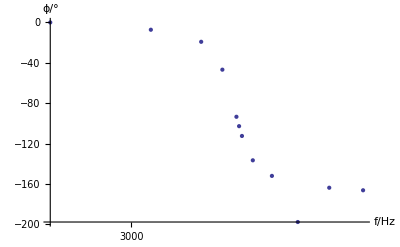

```mathematica
p3=Table[{M[[x,1]],M[[x,1]]*M[[x,3]]*360},{x,2,Length[M]-1}];
ListLogLinearPlot[p3,AxesLabel-> {"f/Hz","ϕ/°"}]
```

```mathematica
End[];
```

## Amplitudengang Widerstand 50Ω

```mathematica
Begin["R2`"];
```

### Messung (Achtung! Konstante Eingangsspannung von 2 V Spitze-Spitze, manuell nachregeln!)

```mathematica
M={{"f/Hz", "Ua/V", "δt", "Ue/V"}, {1906, 2.2*2*50*10^-3, □, 4*0.5}, {3349, 2.8*2*0.1, □, 4*0.5}, {4440, 2.6*2*0.2, □, 4*0.5}, {5000, 3.6*2*0.2, □, 4*0.5}, {5410, 3.8*2*0.2, □, 4*0.5}, {5491, 3.7*2*0.2, □, 4*0.5}, {5580, 3.7*2*0.2, □, 4*0.5}, {5.93*10^3, 3.4*2*0.2, □, 4*0.5}, {6.60*10^3, 2.4*2*0.2, □, 4*0.5}, {7.63*10^3, 3.4*2*0.1, □, 4*0.5}, {9.10*10^3, 2.4*2*0.1, □, 4*0.5}, {11.00*10^3, 1.8*2*0.1, □, 4*0.5}, {30.22*10^3, 2.8*2*50*10^-3, □, 4*0.5}}; dM={{"Δf/Hz", "ΔUa/V", "Δδt", "ΔUe/V"}, {1, □, □, 0.1}, {1, □, □, 0.1}, {1, □, □, 0.1}, {1, □, □, 0.1}, {1, □, □, 0.1}, {1, □, □, 0.1}, {1, □, □, 0.1}, {10, □, □, 0.1}, {10, □, □, 0.1}, {10, □, □, 0.1}, {10, □, □, 0.1}, {10, □, □, 0.1}, {10, □, □, 0.1}};

Ue=4;(*eff, fluke 175*)
due=0.4;
```

### Amplitudengang

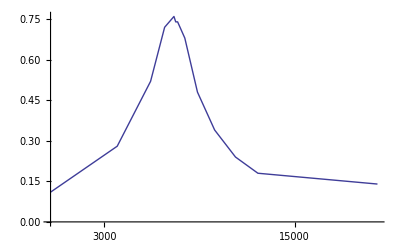

```mathematica
ListLogLinearPlot[Table[{M[[x,1]], M[[x,2]]/M[[x,4]]},{x,2,Length[M]}],Joined -> True]
```

```mathematica
At=Table[Basic`Fdiv[M[[x,2]],dM[[x,2]],M[[x,4]],dM[[x,4]]],{x,2,Length[M]}];
p1 = Table[{{M[[x,1]],10 Log[At[[x-1,1]]]},ErrorBar[dM[[x,1]],At[[x-1,2]]]},{x,2,Length[M]}];
```

```mathematica
Show[ErrorListLogLinearPlot[p1,Joined-> True,PlotStyle-> {Blue}],
LogLinearPlot[{{-3},{0}},{x,Min[M[[2;;Length[M],1]]],Max[M[[2;;Length[M],1]]]},PlotStyle-> {Orange,Black}],
(*ListLogLinearPlot[{{9233.33,10},{9233.33,-50}},Joined ->True,PlotStyle-> {Brown}],*)
AxesLabel -> {"f/Hz","Dämpfung/dB"}]
```

LogLinearPlot::llplim: Range specification {x, Min[M ⟦ 2 ;; Length[M], 1 ⟧], Max[M ⟦ 2 ;; Length[M], 1 ⟧]} is not of the form {x, xmin, xmax} with xmin and xmax positive.

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics-,LogLinearPlot[{{-3},{0}},{x,Min[M⟦2;;Length[M],1⟧],Max[M⟦2;;Length[M],1⟧]},PlotStyle→{Orange,Black}],AxesLabel→{f/Hz,Dämpfung/dB}]

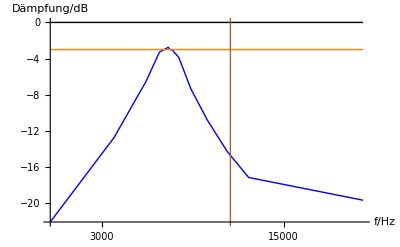

```mathematica
Show[ListLogLinearPlot[Table[{M[[x,1]],10 Log[M[[x,2]]/M[[x,4]]]},{x,2,Length[M]}],Joined-> True,PlotStyle-> {Blue}],
LogLinearPlot[{{-3},{0}},{x,Min[M[[2;;Length[M],1]]],Max[M[[2;;Length[M],1]]]},PlotStyle-> {Orange,Black}],
ListLogLinearPlot[{{9360,10},{9360,-50}},Joined ->True,PlotStyle-> {Brown}],
AxesLabel -> {"f/Hz","Dämpfung/dB"}]
```

### Phasengang

```mathematica
ϕ=Table[Basic`Fmult[M[[x,3]],dM[[x,3]],M[[x,1]],dM[[x,1]]]*360,{x,2,Length[M]}];
p2 = Table[{{M[[x,1]],ϕ[[x-1,1]]},ErrorBar[dM[[x,1]],ϕ[[x-1,2]]]},{x,2,Length[M]}];
```

```mathematica
Show[ErrorListLogLinearPlot[p2,Joined-> True,PlotStyle-> {Blue}],
LogLinearPlot[{{0}},{x,Min[M[[2;;Length[M],1]]],Max[M[[2;;Length[M],1]]]},PlotStyle-> {Orange}],
ListLogLinearPlot[{{9360,-120},{9360,120}},Joined ->True,PlotStyle-> {Brown}],
AxesLabel-> {"f/Hz","ϕ/°"}]
```

LogLinearPlot::llplim: Range specification {x, Min[M ⟦ 2 ;; Length[M], 1 ⟧], Max[M ⟦ 2 ;; Length[M], 1 ⟧]} is not of the form {x, xmin, xmax} with xmin and xmax positive.

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics-,LogLinearPlot[{{0}},{x,Min[M⟦2;;Length[M],1⟧],Max[M⟦2;;Length[M],1⟧]},PlotStyle→{Orange}],-Graphics-,AxesLabel→{f/Hz,ϕ/°}]

```mathematica
p3=Table[{M[[x,1]],M[[x,1]]*M[[x,3]]*360},{x,2,Length[M]-1}];
ListLogLinearPlot[p3,AxesLabel-> {"f/Hz","ϕ/°"}]
```

-Graphics-

```mathematica
End[];
```